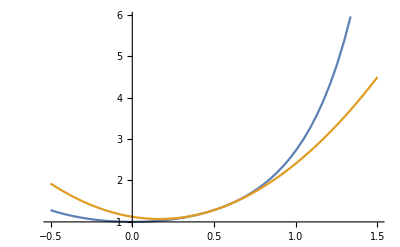

```mathematica
f[x_]:=Exp[x^2];
m[y_,x_]:=Evaluate[(f[x]+Evaluate[D[f[p],p]/.p->x] p + Evaluate[D[f[p],{p,2}]/.p->x]/2 p^2)/.p->y]
x0=1/2;
Plot[{f[x],m[x-x0,x0]},{x,x0-1,x0+1}](*,PlotRange->{f[x0]-1,f[x0]+1}]*)
```

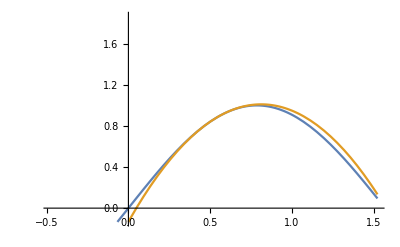

```mathematica
f[x_]:=Sin[2x];
m[y_,x_]:=Evaluate[(f[x]+Evaluate[D[f[p],p]/.p->x] p + Evaluate[D[f[p],{p,2}]/.p->x]/2 p^2)/.p->y]
x0=Pi/6;
Plot[{f[x],m[x-x0,x0]},{x,x0-1,x0+1},PlotRange->{f[x0]-1,f[x0]+1}]
```